## Hybrid Functions Razzaghi

```mathematica
bb[nn_Integer,NN_Integer,mm_Integer,MM_Integer,tt_?NumberQ,tf_?NumberQ]:=
If[((nn-1)/NN)*tf<=tt<(nn/NN)*tf,LegendreP[mm,((2*NN)/tf)*tt- 2*nn+1],0]/;And[nn≤NN,mm<=MM,0<=tt<=tf]
```

```mathematica
symbb[nn_Integer,NN_Integer,mm_Integer,MM_Integer,tt_Symbol,tf_?NumberQ]:=
If[((nn-1)/NN)*tf<=tt<(nn/NN)*tf,LegendreP[mm,((2*NN)/tf)*tt- 2*nn+1],0]/;And[nn≤NN,mm<=MM]
```

```mathematica
forProd[MM_Integer]:=
With[{polys=
LegendreP[#,xx]&/@Range[0,2*(MM-1)]},With[{polyProds=Select[getUpper[Outer[Times,polys[[Range[MM]]],polys[[Range[MM]]]]],polyOrder[#] < 2*MM -1&]},With[{someCoeffs=Table[Unique[],{Length[polys]}]},
toSolve[someCoeffs,polys,#]&/@polyProds]]]
```

```mathematica
forProd[MM_Integer,qq_Integer]:=
With[{polys=
LegendreP[#,xx]&/@Range[0,2*(MM-1)]},With[{polyProds=Select[Flatten[getUpper[kron[IdentityMatrix[qq],Outer[Times,polys[[Range[MM]]],polys[[Range[MM]]]]]]],polyOrder[#] < 2*MM -1&]},With[{someCoeffs=Table[Unique[],{Length[polys]}]},
toSolve[someCoeffs,polys,#]&/@polyProds]]]
```

```mathematica
toSolve[coeffs_List,basePolys_List,polyNow_]:=
With[{byPow=CoefficientList[(coeffs .basePolys),xx]},
With[{pNowbyPow=Coefficient[polyNow,xx,#]&/@Range[0,Length[byPow]-1]},Sow[eqns=Thread[byPow==pNowbyPow]];
Solve[eqns,coeffs]]]
```

```mathematica
getUpper[theMat_?MatrixQ]:=With[{theDim=Length[theMat]},
Flatten[MapIndexed[#[[Range[#2[[1]],theDim]]]&,theMat]]]
```

```mathematica
polyOrder[aPoly_]:=Length[CoefficientList[aPoly,xx]]-1
```

```mathematica
pMat[NN_Integer,MM_Integer,tf_?NumberQ]:=With[{theE=eMat[NN,MM,tf],theH=hMat[NN,MM,tf]},
ArrayFlatten[aRow[#,NN,theE,theH]&/@Range[0,NN-1]]]
```

```mathematica
oldP0[NN_Integer]:=With[{above=DiagonalMatrix[Table[1,{NN-#}],#]&/@Range[NN-1]},
(Plus @@ above)+(1/2)*IdentityMatrix[NN]]
```

```mathematica
oldP[NN_Integer,MM_Integer]:=With[{abvList=Table[1/(2*(2*ii+1)),{ii,0,MM,
```

```mathematica
oldP0[4]
```

{{1/2,1,1,1},{0,1/2,1,1},{0,0,1/2,1},{0,0,0,1/2}}

```mathematica
aRow[zeroes_Integer,theN_Integer,eM_?MatrixQ,hM_?MatrixQ]:=
With[{theM=Length[eM]},With[{theZm=ConstantArray[0,{theM,theM}]},
Join[Table[theZm,{zeroes}],{eM},Table[hM,{theN-zeroes-1}]]]]
```

```mathematica
hMat[NN_Integer,MM_Integer,tf_?NumberQ]:=With[{onD=Join[{1},Table[0,{MM-1}]]},
(tf/NN)*DiagonalMatrix[onD]]
```

```mathematica
eMat[NN_Integer,MM_Integer,tf_?NumberQ]:=With[{offDPlus=Table[1/(2*ii+1),{ii,0,(MM-2)}],offDMinus=Table[-1/(2*ii+1),{ii,1,(MM-1)}],onD=Join[{1},Table[0,{MM-1}]]},
(tf/(2*NN))*(DiagonalMatrix[offDPlus,1]+DiagonalMatrix[offDMinus,-1]+DiagonalMatrix[onD])]
```

```mathematica
conbTbMat[MM_Integer]:=
With[{thebtb=Map[#[[2]]&,Flatten[forProd[MM],1],{-2}][[All,Range[MM]]]},With[{upperT=thebtb . Transpose[{Table[bb[ii],{ii,0,MM-1}]}]},Flatten[upperT]]]
```

```mathematica
conbTbMat[MM_Integer,qq_Integer]:=
With[{thebtb=Map[#[[2]]&,Flatten[forProd[MM,qq],1],{-2}][[All,Range[MM]]]},With[{upperT=thebtb . Transpose[{Table[bb[ii],{ii,0,MM-1}]}]},Flatten[upperT]]]
```

```mathematica
upperTToFull[upperT_List]:=
With[{nn=cmpN[upperT]},With[{justUp=prtnUpper[{nn,upperT,{}}][[-1]]},
(justUp+Transpose[justUp]-DiagonalMatrix[Diagonal[justUp]])]]
```

```mathematica
prtnUpper[{nn_Integer,aList_List,theRes_List}]:=
With[{nNow=cmpN[aList]},If[nNow==0,{nn,aList,theRes},
prtnUpper[{nn,Drop[aList,nNow],Append[theRes,augZeroes[nn-nNow,Part[aList,Range[nNow]]]]}]]]
```

```mathematica
tabb[MM_Integer]:=
With[{thebtb=Map[#[[2]]&,Flatten[forProd[MM],1],{-2}][[All,Range[MM]]]},With[{upperT=thebtb . Transpose[{Table[bb[ii],{ii,0,MM-1}]}]},Flatten[upperT]]]
```

```mathematica
cmpN[upperT_List]:=nnVal/.Flatten[Solve[nnVal/2*(1+nnVal)==Length[Flatten[upperT]] &&Abs[nnVal]==nnVal]]
```

```mathematica
augZeroes[numZ_Integer,aRow_List]:=
Join[Table[0,{numZ}],aRow]
```

```mathematica
augMatForDiag[pre_Integer,aMat_?MatrixQ,post_Integer]:=
With[{aZero=ConstantArray[0,{Length[aMat],Length[aMat[[1]]]}]},
Join[Table[aZero,{pre}],{aMat},Table[aZero,{post}]]]
```

```mathematica
mltb[MM_Integer]:=
With[{theMlt=upperTToFull[conbTbMat[MM]].Table[{bb[ii,jj]},{jj,0,MM-1}]},With[{allCols=coeffOfRow[theMlt,bb[#]]&/@Range[0,MM-1]},Transpose[Join[allCols]]]]
```

```mathematica
mltb[MM_Integer,qq_Integer]:=
With[{theMlt=upperTToFull[conbTbMat[MM,qq]].Table[{bb[ii,Mod[jj,MM]]},{jj,0,qq*MM-1}]},With[{allCols=coeffOfRow[theMlt,bb[#]]&/@Range[0,MM-1]},Transpose[Join[allCols]]]]
```

```mathematica
coeffOfRow[aRow_List,theVar_]:=
Flatten[Coefficient[aRow,theVar]]
```

```mathematica
mltb[2]
```

{{bb[ii,0],bb[ii,1]},{1/3 bb[ii,1],bb[ii,0]}}

```mathematica
bSubs[NN_Integer,bVec_?VectorQ]:=
With[{MM=Length[bVec]/NN},
With[{thebs=Flatten[Table[bb[ii,jj],{ii,1,NN},{jj,0,MM-1}]]},
Thread[thebs->bVec]]/;IntegerQ[Length[bVec]/NN]]
```

```mathematica
bSubs[NN_Integer,bMat_List]:=
With[{MM=Length[bMat[[1,1]]]/NN},
With[{thebs=Flatten[Table[bb[ii,jj],{ii,1,NN},{jj,0,MM-1}]]},
Thread[thebs->#]&/@Flatten[bMat,1]]/;IntegerQ[Length[bMat[[1,1]]]/NN]]
```

```mathematica
makebTilde[NN_Integer,bVec_?VectorQ]:=
With[{MM=Length[bVec]/NN},With[{bs=bSubs[NN,bVec],lilb=mltb[MM]},
ArrayFlatten[prepRow[#,NN,bs,lilb]&/@Range[NN]]]]/;IntegerQ[Length[bVec]/NN]
```

```mathematica
makeFTilde[NN_Integer,fMat_List]:=
With[{MM=Length[fMat[[1,1]]]/NN},
With[{qq=Length[fMat[[1]]],ll=Length[fMat]},With[{bs=bSubs[NN,fMat],lilb=mltb[MM,qq]},
ArrayFlatten[prepRow[#,NN,bs,lilb]&/@Range[NN]]]]]/;IntegerQ[Length[fMat[[1,1]]]/NN]
```

```mathematica
makeEFTilde[NN_Integer,eMat_List]:=
With[{ll=Length[eMat]},With[{theLot=Map[makebTilde[NN,#1]&,eMat,{2}]},ArrayFlatten[theLot]]]/;IntegerQ[Length[eMat[[1,1]]]/NN]
```

```mathematica
Map[ff,IdentityMatrix[4],{1}]
```

{ff[{1,0,0,0}],ff[{0,1,0,0}],ff[{0,0,1,0}],ff[{0,0,0,1}]}

```mathematica
prepRow[iVal_Integer,nVal_Integer,bs_List,lilb_?MatrixQ]:=
augMatForDiag[iVal-1,(lilb/.ii->iVal)/.bs,nVal-iVal]
```

```mathematica
kron[aa_?MatrixQ,bb_?MatrixQ]:=ArrayFlatten[Outer[Times,aa,bb]]
```

```mathematica
makebVec[NN_Integer,MM_Integer,tf_?NumberQ]:=Transpose[{Flatten[Table[bb[ii,NN,jj,MM,tt,tf],{ii,NN},{jj,0,MM-1}]]}]
```

```mathematica
makebHat[theDim_Integer,bVec_?MatrixQ]:=
kron[IdentityMatrix[theDim],bVec]
```

```mathematica
bv=makebVec[2,3,1]
```

{{bb[1,2,0,3,tt,1]},{bb[1,2,1,3,tt,1]},{bb[1,2,2,3,tt,1]},{bb[2,2,0,3,tt,1]},{bb[2,2,1,3,tt,1]},{bb[2,2,2,3,tt,1]}}

```mathematica
makeInitCondD[NN_Integer,MM_Integer]:=With[{onlyOne={Join[{1},Table[0,{MM-1}]]}},
Transpose[ArrayFlatten[{Table[onlyOne,{NN}]}]]]
```

```mathematica
dynamicsMats[NN_Integer,MM_Integer,EE_List,FF_List,dd_?MatrixQ,tf_?NumberQ]:=With[{ll=Length[EE],qq=Length[FF],bs=Flatten[Table[bb[nn,NN,mm,MM,tt,tf],{nn,1,NN},{mm,0,MM-1}]]},
With[{eeTilde=makeEFTilde[NN,EE],ffTilde=makeEFTilde[NN,FF],theP=pMat[NN,MM,tf]},{bs,Transpose[eeTilde]. kron[IdentityMatrix[ll],Transpose[theP]]-IdentityMatrix[ll*MM*NN],Transpose[ffTilde],Transpose[eeTilde].dd}]]
```

```mathematica
dynamicsMats[NN_Integer,MM_Integer,EE_List,FF_List,dd_?MatrixQ,tf_?NumberQ]:=With[{ll=Length[EE],qq=Length[FF],bs=Flatten[Table[bb[nn,NN,mm,MM,tt,tf],{nn,1,NN},{mm,0,MM-1}]]},
With[{eeTilde=makeEFTilde[NN,EE],ffTilde=makeEFTilde[NN,FF],theP=pMat[NN,MM,tf]},{bs,eeTilde. kron[IdentityMatrix[ll],Transpose[theP]]-IdentityMatrix[ll*MM*NN],ffTilde,eeTilde.dd}]]
```

```mathematica
cmpD[NN_Integer,MM_Integer,tf_Integer]:=With[{elems=(tf/NN)*Table[(1/(2*ii-1)),{ii,1,MM}]},DiagonalMatrix[elems]]
```

```mathematica
blockDiagonalMatrix[NN_Integer,theD_?MatrixQ]:=Module[{r,c,i,j},{r,c}=Dimensions[theD];
ArrayFlatten[Table[If[i==j,theD,ConstantArray[0,{r,c}]],{i,NN},{j,NN}]]]
```

```mathematica
cmpJ[dd_?MatrixQ,pp_?MatrixQ,xx_?MatrixQ,btf_?MatrixQ,ss_?MatrixQ,ll_?MatrixQ,qMat_?MatrixQ,rMat_?MatrixQ]:=
With[{dPlusP=dd+ Transpose[pp ]. xx
```

## tests

```mathematica
someBs=Table[bb[nn,4,mm,3,tt,1],{nn,1,4},{mm,0,2}];
```

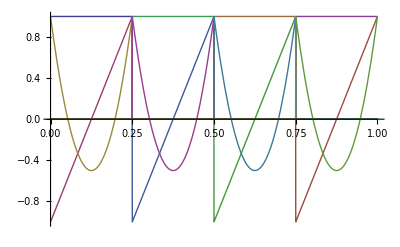

```mathematica
Plot[someBs,{tt,0,1}]
```

```mathematica
someSymBs=Flatten[Table[symbb[nn,4,mm,3,tt,1],{nn,1,4},{mm,0,2}]];
```

```mathematica
fBs=Transpose[{Flatten[someBs]}]
```

{{bb[1,4,0,3,tt,1]},{bb[1,4,1,3,tt,1]},{bb[1,4,2,3,tt,1]},{bb[2,4,0,3,tt,1]},{bb[2,4,1,3,tt,1]},{bb[2,4,2,3,tt,1]},{bb[3,4,0,3,tt,1]},{bb[3,4,1,3,tt,1]},{bb[3,4,2,3,tt,1]},{bb[4,4,0,3,tt,1]},{bb[4,4,1,3,tt,1]},{bb[4,4,2,3,tt,1]}}

```mathematica
NIntegrate[fBs .Transpose[fBs],{tt,0,1}]//TableForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tt near {tt} = {0.24021883335946762`}. NIntegrate obtained 5.11743×10^-17 and 1.12384×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tt near {tt} = {2.76990133638922`*^-15}. NIntegrate obtained 2.60209×10^-18 and 2.99817×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tt near {tt} = {0.6660311666405324`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

0.25 | 5.11743×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5.11743×10^-17 | 0.0833333 | 1.73472×10^-18 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.73472×10^-18 | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.25 | 3.46945×10^-18 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 3.46945×10^-18 | 0.0833333 | -2.60209×10^-18 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -2.60209×10^-18 | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 3.46945×10^-18 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 3.46945×10^-18 | 0.0833333 | 2.60209×10^-18 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.60209×10^-18 | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | -3.46945×10^-18 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -3.46945×10^-18 | 0.0833333 | -2.60209×10^-18
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.60209×10^-18 | 0.05

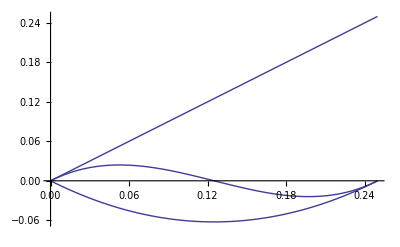

```mathematica
Plot[NIntegrate[(sip=Transpose[{Flatten[someBs]}][[Range[3]]]),{tt,0,tVal}],{tVal,0,0.2499}]
```

```mathematica
someBs[[1,1]]
```

bb[1,4,0,3,tt,1]

## example 1

```mathematica
abon={1,0,0};
```

```mathematica
tryE=Transpose[{{Join[0*abon,0*abon,0*abon,0*abon],Join[1*abon,1*abon,1*abon,1*abon]},{Join[0*abon,0*abon,0*abon,0*abon],Join[-1*abon,-1*abon,-1*abon,-1*abon]}}];
```

```mathematica
tryF={{Join[0*abon,0*abon,0*abon,0*abon]},{Join[1*abon,1*abon,1*abon,1*abon]}};
```

```mathematica
Dimensions[tryF]
```

{2,1,12}

```mathematica
theU=Transpose[{Table[Random[Integer,{-5,5}],{12}] }];
```

```mathematica
theInit=Join[0*makeInitCondD[4,3],10*makeInitCondD[4,3]];
```

```mathematica
theInit
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{10},{0},{0},{10},{0},{0},{10},{0},{0},{10},{0},{0}}

```mathematica
theLot={bs,mltX,mltU,dTerm}=dynamicsMats[4,3,tryE,tryF,theInit,1];
```

```mathematica
Dimensions/@ theLot
```

{{12},{24,24},{24,12},{24,1}}

```mathematica
dTerm
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-10},{0},{0},{-10},{0},{0},{-10},{0},{0},{-10},{0},{0}}

```mathematica
theX=Inverse[mltX] . ((-1)*(mltU.theU + dTerm))//N;
```

```mathematica
thebasis=kron[IdentityMatrix[2],Transpose[{bs}]];
```

```mathematica
bothxs={x1,x2}=Transpose[thebasis]. theX//Chop
```

{{0},{-6.08125 bb[1,4,0,3,tt,1]+3.80619 bb[1,4,1,3,tt,1]+1.84141 bb[1,4,2,3,tt,1]-10.0099 bb[2,4,0,3,tt,1]+5.24577 bb[2,4,1,3,tt,1]-0.218574 bb[2,4,2,3,tt,1]-7.13279 bb[3,4,0,3,tt,1]-1.13222 bb[3,4,1,3,tt,1]-0.952824 bb[3,4,2,3,tt,1]+0.748116 bb[4,4,0,3,tt,1]+0.855594 bb[4,4,1,3,tt,1]-2.03565 bb[4,4,2,3,tt,1]}}

```mathematica
bothxs[[2]]/.tt->.0
```

{-8.04604}

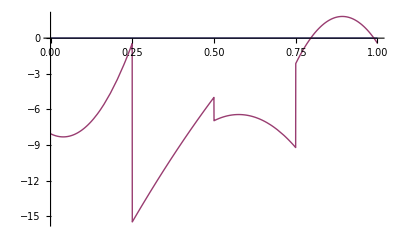

```mathematica
Plot[bothxs,{tt,0,1}]
```

```mathematica
Dimensions[theBasis]
```

{}

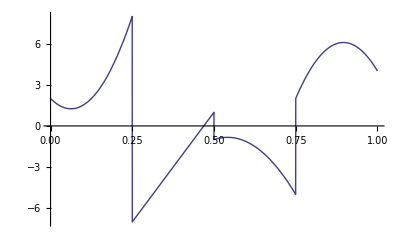

```mathematica
Plot[Transpose[theU ].thebasis[[12+Range[12],{2}]],{tt,0,1}]
```

```mathematica
c1t={{c110,c111,c112,c120,c121,c122,c130,c131,c132,c140,c141,c142}};
```

```mathematica
c2t={{c210,c211,c212,c220,c221,c222,c230,c231,c232,c240,c241,c242}};
```

```mathematica
ut={{u10,u11,u12,u20,u21,u22,u30,u31,u32,u40,u41,u42}};
```

```mathematica
uu=ut . fBs;
```

{{u10 bb[1,4,0,3,tt,1]+u11 bb[1,4,1,3,tt,1]+u12 bb[1,4,2,3,tt,1]+u20 bb[2,4,0,3,tt,1]+u21 bb[2,4,1,3,tt,1]+u22 bb[2,4,2,3,tt,1]+u30 bb[3,4,0,3,tt,1]+u31 bb[3,4,1,3,tt,1]+u32 bb[3,4,2,3,tt,1]+u40 bb[4,4,0,3,tt,1]+u41 bb[4,4,1,3,tt,1]+u42 bb[4,4,2,3,tt,1]}}

```mathematica
(-1)*(c2t.theP+e2t)//Dimensions
```

{1,12}

```mathematica
x1dot=c1t .  fBs;
```

```mathematica
x2dot=c2t .  fBs;
```

```mathematica
theP=pMat[4,3,1];
```

```mathematica
e2t=Transpose[10*makeInitCondD[4,3]];
```

```mathematica
x1=c1t.theP.fBs;
```

```mathematica
x2=(c2t.theP+e2t).fBs;
```

```mathematica
eqns=Join[Thread[Flatten[c1t]==Flatten[c2t.theP+e2t]],Thread[Flatten[c2t]==Flatten[(-1)*(c2t.theP+e2t)+ut]]]//N;
```

```mathematica
soln=Flatten[Solve[eqns,Flatten[Join[c1t,c2t]]]//N];
```

```mathematica
utSubs=Thread[Flatten[ut]->Table[Random[Integer,{-5,5}],{12}]];
```

```mathematica
soln/.utSubs
```

{c110→9.27564,c111→-0.557832,c112→0.0649097,c120→7.29488,c121→-1.38438,c122→0.099349,c130→5.55869,c131→-0.49224,c132→0.103843,c140→4.612,c141→-0.70077,c142→0.0291987,c210→-5.27564,c211→1.55783,c212→-4.06491,c220→-10.2949,c221→2.38438,c222→3.90065,c230→-3.55869,c231→2.49224,c232→1.89616,c240→-4.612,c241→0.70077,c242→4.9708}

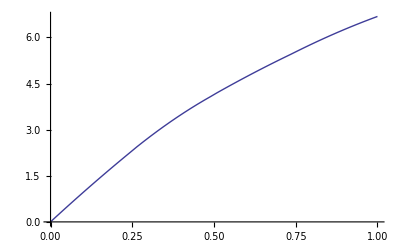

```mathematica
Plot[thex1=x1/.soln/.utSubs,{tt,0,1}]
```

```mathematica
x1/.soln/.utSubs
```

{{1.1827 bb[1,4,0,3,tt,1]+1.15783 bb[1,4,1,3,tt,1]-0.023243 bb[1,4,2,3,tt,1]+3.28845 bb[2,4,0,3,tt,1]+0.909376 bb[2,4,1,3,tt,1]-0.0576824 bb[2,4,2,3,tt,1]+4.85798 bb[3,4,0,3,tt,1]+0.69224 bb[3,4,1,3,tt,1]-0.02051 bb[3,4,2,3,tt,1]+6.138 bb[4,4,0,3,tt,1]+0.57577 bb[4,4,1,3,tt,1]-0.0291987 bb[4,4,2,3,tt,1]}}

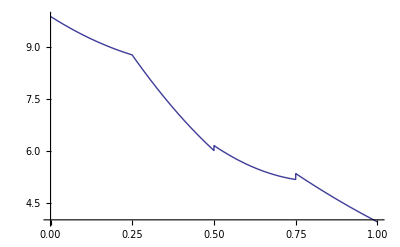

```mathematica
Plot[thex2=x2/.soln/.utSubs,{tt,0,1}]
```

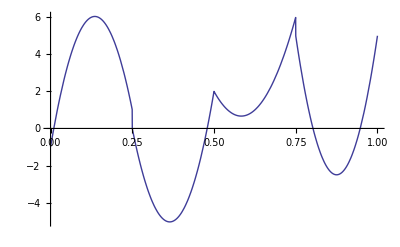

```mathematica
Plot[theu=ut.fBs/.soln/.utSubs,{tt,0,1}]
```

## jung, teranishi and watanabe

```mathematica
jtwSubs={lambda->(0.048/4)^2,beta->0.990,sigma->0.157,kappa->0.024,rnInf->0.011,rho->0.5,eps0->(-.1)}
```

{lambda→0.000144,beta→0.99,sigma→0.157,kappa→0.024,rnInf→0.011,rho→0.5,eps0→-0.1}

```mathematica
eqns={pi[tt]+phi2[tt],lambda*xx[tt]+phi1[tt]-kappa*phi2[tt] ,ii[tt]*phi1[tt],xx[tt] -(xx[tt+1]- (1/sigma)*((ii[tt]-pi[tt+1])-rn[tt])),pi[tt]-(kappa*xx[tt] + beta* pi[tt+1])};
cons={ii[tt] ≥ 0,phi1[tt]≥0}
```

{ii[tt]≥0,phi1[tt]≥0}

```mathematica
Solve[eqns/.tt->Infinity,{pi[Infinity],phi1[Infinity],phi2[Infinity],xx[Infinity],ii[Infinity]}]
```

$Aborted

```mathematica
rnVals[tt_?NumberQ]:= rho^tt*eps0 +rnInf
```

```mathematica
bigN=20;bigM=3;bigT=20.1;
forR=Table[rnVals[ii],{ii,0,bigT-1}];
moreBs=Transpose[{Flatten[Table[bb[ii,bigN,jj,bigM,tt,bigT],{ii,1,bigN},{jj,0,bigM-1}]]}];
piCoeffs=Table[Unique["piCf"],{Length[moreBs]}];
phi1Coeffs=Table[Unique["phi1Cf"],{Length[moreBs]}];
phi2Coeffs=Table[Unique["phi2Cf"],{Length[moreBs]}];xxCoeffs=Table[Unique["xxCf"],{Length[moreBs]}];
iiCoeffs=Table[Unique["iiCf"],{Length[moreBs]}];(*rnCoeffs=Table[Unique["rnCf"],{Length[moreBs]}];*)
rnCoeffs=Table[0,{Length[moreBs]}];rnCoeffs[[Range[1,Length[moreBs],bigM]]]=forR/.jtwSubs;
tryBFSubs={pi[tt]->(piCoeffs . moreBs)[[1]],pi[tt+1]->(((piCoeffs . moreBs)[[1]])/.tt->tt+1),phi1[tt]->(phi1Coeffs.moreBs)[[1]],phi2[tt]->(phi2Coeffs.moreBs)[[1]],xx[tt]->xxCoeffs.moreBs,xx[tt+1]->(((xxCoeffs.moreBs)[[1]])/.tt->tt+1),ii[tt]->(iiCoeffs.moreBs)[[1]],rn[tt]->rnCoeffs . moreBs};
```

```mathematica
forMin=((eqns.eqns)/.tryBFSubs/.jtwSubs)[[1]];
notForMin=((eqns)/.tryBFSubs/.jtwSubs);
consForMin=And@@Flatten[cons/.Flatten[tryBFSubs]/.Flatten[jtwSubs]];
```

```mathematica
{val,theSubs}=FindMinimum[Plus @@ Table[forMin/.tt->tVal,{tVal,9}],Transpose[{Join[piCoeffs,phi1Coeffs,phi2Coeffs,xxCoeffs,iiCoeffs],Flatten[Table[rnCoeffs,{5}]]}],MaxIterations->20000];
```

```mathematica
val
```

4.21363×10^-11

```mathematica
ii[tt]/.tryBFSubs/.theSubs/.tt->3
```

-0.0113927

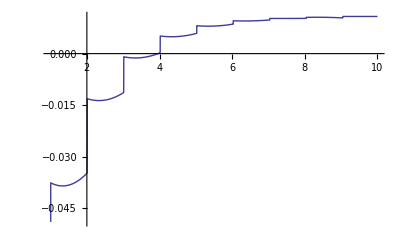

```mathematica
Plot[ii[tt]/.tryBFSubs/.theSubs,{tt,1,10}]
```

```mathematica
{val,theSubs}=FindMinimum[Plus @@ Table[forMin/.tt->tVal,{tVal,9}],Transpose[{Join[piCoeffs,phi1Coeffs,phi2Coeffs,xxCoeffs,iiCoeffs],Flatten[Table[rnCoeffs,{5}]]}],MaxIterations->20000];
```

FindMinimum::nrnum: The function value 1.` iiCf1143^2 phi1Cf1175^2 + 1.` iiCf1144^2 phi1Cf1176^2 + « 8 » + « 35 » is not a real number at {piCf1207, piCf1208, piCf1209, piCf1210, piCf1211, piCf1212, piCf1213, piCf1214, piCf1215, piCf1216, « 290 »} = {-0.08900000000000001`, 0.`, 0.`, -0.03900000000000001`, « 3 », 0.`, 0.`, -0.0015000000000000013`, « 290 »}.

Set::shape: Lists {val, theSubs} and FindMinimum[Plus @@ Table[forMin/. tt → tVal, {tVal, 9}], Transpose[{Join[« 1 »], « 1 »}], MaxIterations → 20000] are not the same shape.

FindMinimum::nrnum: The function value 1.` iiCf1143^2 phi1Cf1175^2 + 1.` iiCf1144^2 phi1Cf1176^2 + « 8 » + « 35 » is not a real number at {piCf1207, piCf1208, piCf1209, piCf1210, piCf1211, piCf1212, piCf1213, piCf1214, piCf1215, piCf1216, « 290 »} = {-0.08900000000000001`, 0.`, 0.`, -0.03900000000000001`, « 3 », 0.`, 0.`, -0.0015000000000000013`, « 290 »}.

```mathematica
{valcon,theSubscon}=hep=FindMinimum[{Plus @@ Table[forMin/.tt->tVal,{tVal,9}],And @@Table[consForMin/.tt->tVal,{tVal,9}](*,consForMin*)},Transpose[{Join[piCoeffs,phi1Coeffs,phi2Coeffs,xxCoeffs,iiCoeffs],Flatten[Table[rnCoeffs,{5}]]}],MaxIterations->20000];
```

Set::shape: Lists {valcon, theSubscon} and FindMinimum[« 1 »] are not the same shape.

```mathematica
valcon
```

9.99055×10^-7

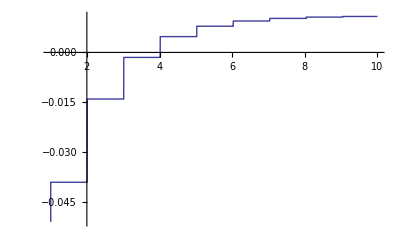

```mathematica
Plot[rn[tt]/.tryBFSubs/.theSubscon,{tt,1,10}]
```

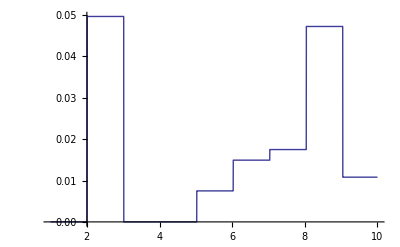

```mathematica
Plot[ii[tt]/.tryBFSubs/.theSubscon,{tt,1,10}]
```